div: 6.

reminder: 2.00001

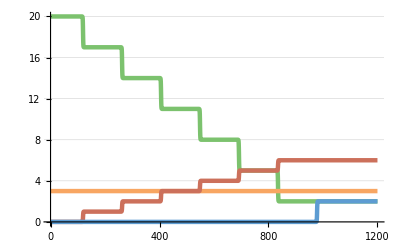

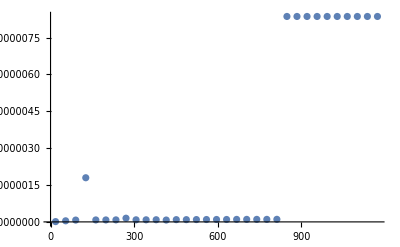

```mathematica
Get[NotebookDirectory[]<>"/division.m"]
rsys=DiscreteDivisionRsys[20,3];
tmax=1200;
sol=SimulateRxnsys[ExpandDiscreteRsys[rsys], tmax];
Print["div: " <> ToString[EvaluateRxnAtPoint[sol,q,tmax]]];
Print["reminder: " <> ToString[EvaluateRxnAtPoint[sol,r,tmax]]];
PlotForPaper[Evaluate[{a[t],b[t],q[t],r[t]}/.sol], tmax, 200]

errorMap=EvaluateError[rsys, tmax];
aErrorList=errorMap[a]/.{resultMap_}:>{resultMap["time"],resultMap["error"]};
ListPlot[aErrorList,Ticks->{Range[0,tmax,100],Automatic}]
```